# Figure 2

Data are imported from julia code https://github.com/djuliannader/RabiModel

#### Data

```mathematica
(*R=50*)
DatNegR50={{0,0},{0.05,0},{0.1,0},{0.15,0},{0.2,0},{0.25,0},{0.3,0},{0.35,0},{0.4,0},{0.45,0},{0.5,0},{0.55,0},{0.6,0},{0.65,0},{0.7,0},{0.75,0},{0.8,0},{0.85,0},{0.9,1*10^(-6)},{0.95,9.6*10^(-5)},{1,0.0028721938315612316},{1.025,0.012356555259824376},{1.05,0.045046985365931436},{1.075,0.1307916991903315},{1.1,0.2733874102764575},{1.125,0.38936523329485073},{1.15,0.4362242778645884},{1.175,0.4460885111407016},{1.2,0.44040837488184037},{1.25,0.41433117514498274},{1.3,0.38455247706474105},{1.35,0.35639368013159256},{1.4,0.33087341966824346},{1.45,0.30794844862649895},{1.5,0.28734309709107686},{1.55,0.2687654993931692},{1.6,0.25195532747756655},{1.65,0.23669221450165723},{1.7,0.22278777508091752},{1.75,0.21007710233871846},{1.8,0.19843810833889042},{1.85,0.1869269263497304},{1.9,0.17789491169926075},{1.95,0.16879059428329657},{2,0.1603653371543292}};
DatPurR50={{0,1},{0.05,0.9999759424382747},{0.1,0.9999034272558528},{0.15,0.9997814087135403},{0.2,0.9996080810591991},{0.25,0.999380776762398},{0.3,0.9990958075749397},{0.35,0.9987482279968808},{0.4,0.9983314878694249},{0.45,0.9978369196052229},{0.5,0.9972529689231903},{0.55,0.996564011762457},{0.6,0.9957484746508471},{0.65,0.994775725143428},{0.7,0.9936006656401877},{0.75,0.9921537418880904},{0.8,0.9903210142961318},{0.85,0.9879003610322292},{0.9,0.9844922503337201},{0.95,0.9791771590785479},{1,0.9693224813794615},{1.025,0.9603014280895678},{1.05,0.9450674965437998},{1.075,0.9184515579592468},{1.1,0.8785402990262056},{1.125,0.8367710422842245},{1.15,0.8026871790347999},{1.175,0.7750621854308072},{1.2,0.7514555074649951},{1.25,0.7121302675708026},{1.3,0.6805020299580149},{1.35,0.6546746928544679},{1.4,0.6333677520262117},{1.45,0.6156417139444618},{1.5,0.600786672980406},{1.55,0.5882553764843841},{1.6,0.5776228874870241},{1.65,0.5685489740866942},{1.7,0.5607683254538206},{1.75,0.5540913609047422},{1.8,0.5482842532028399},{1.85,0.547209527765898},{1.9,0.538855080298695},{1.95,0.5350590376220995},{2,0.5316210729540178}};
DatCocR50={{0,0.7499999999999998/(3*(0.4999999999999999)^2)},{0.05,0.75187881532106897/(3*0.5006258878683949^2)},{0.1,0.7575702173461962/(3*0.5025171970312261^2)},{0.15,0.7672430711295672/(3*0.5057156865326069^2)},{0.2,0.7811926858842599/(3*0.5102937934627627^2)},{0.25,0.7998636425150817/(3*0.5163592513308773^2)},{0.3,0.8238862783538767/(3*0.5240623516549455^2)},{0.35,0.8541326243608005/(3*0.5336068437488745^2)},{0.4,0.8918015616587754/(3*0.5452661080007922^2)},{0.45,0.9385498275352047/(3*0.5594073064848732^2)},{0.5,0.996697933655965/(3*0.5765280821003401^2)},{0.55,1.0695636551744288/(3*0.5973137902315173^2)},{0.6,1.1620228587208135/(3*0.6227297910696789^2)},{0.65,1.2814970798851983/(3*0.6541765798996451^2)},{0.7,1.4397927565972026/(3*0.693764110355717^2)},{0.75,1.6567702540922875/(3*0.744828134343037^2)},{0.8,1.9683184699322553/(3*0.8129808049796601^2)},{0.85,2.445693875973183/(3*0.9084715246222741^2)},{0.9,3.2496856720845577/(3*1.0522287176106724^2)},{0.95,4.8151561325445025/(3*1.2942812620568696^2)},{1,8.676709177081129/(3*1.7849882071835745^2)},{1.025,13.191130472442584/(3*2.2674391149095015^2)},{1.05,22.631175113336358/(3*3.1320410019378047^2)},{1.075,43.84346854342823/(3*4.753957890115041^2)},{1.1,86.54058048100657/(3*7.410067949519209^2)},{1.125,148.84634210202725/(3*10.493667021321095^2)},{1.15,220.15169859326082/(3*13.300979254959833^2)},{1.175,298.0586531970737/(3*15.832025942614708^2)},{1.2,383.911126000021/(3*18.228560986896323^2)},{1.25,582.5198428458652/(3*22.858291957216757^2)},{1.3,818.4428985824297/(3*27.38980353593512^2)},{1.35,1092.5948047408485/(3*31.877910055932638^2)},{1.4,1406.17855195663/(3*36.35409907025217^2)},{1.45,1760.7759077694393/(3*40.84098049841334^2)},{1.5,2158.2884623808554/(3*45.35588629225168^2)},{1.55,2600.874994032024/(3*49.912668152907095^2)},{1.6,3090.9451497954847/(3*54.522313513662965^2)},{1.65,3631.0354456672376/(3*59.19451141631789^2)},{1.7,4223.937966769323/(3*63.936610365068354^2)},{1.75,4964.608564499193/(3*69.40134670548123^2)},{1.8,5580.401624562337/(3*73.65252497015442^2)},{1.85,6452.280035530374/(3*78.98110097928066^2)},{1.9,7184.645185183218/(3*83.71637627393808^2)},{1.95,8089.722951897358/(3*88.8786945024876^2)},{2.0,9063.371818421145/(3*94.15939241686685^2)}};
(*R=100*)
DatNegR100={{0,0},{0.05,0},{0.1,0},{0.15,0},{0.2,0},{0.25,0},{0.3,0},{0.35,0},{0.4,0},{0.45,0},{0.5,0},{0.55,0},{0.6,0},{0.65,0},{0.7,0},{0.75,0},{0.8,0},{0.85,0},{0.9,0},{0.95,1.9*10^(-5)},{1,0.00352991345976994},{1.025,0.030395052099949194},{1.05,0.16994734619626084},{1.075,0.4084990889013467},{1.1,0.4951335362409819},{1.125,0.5006191493627601},{1.15,0.48681954343363354},{1.175,0.4681538977706101},{1.2,0.4489441006974306},{1.25,0.4129849354026838},{1.3,0.38113406266114835},{1.35,0.35263284981942244},{1.4,0.32781379856719917},{1.45,0.3053228932107588},{1.5,0.2850804145723995},{1.55,0.26656609689781363},{1.6,0.2480970185098632},{1.65,0.23207183786995234},{1.7,0.21943236369303798},{1.75,0.2062951673978768},{1.8,0.19439519895389978},{1.85,0.1848269263497304},{1.9,0.17489491169926075},{1.95,0.16579059428329657},{2,0.1573653371543292}};
DatPurR100={{0,1},{0.05,0.9999759424382747},{0.1,0.9999034272558528},{0.15,0.9997814087135403},{0.2,0.9996080810591991},{0.25,0.999380776762398},{0.3,0.9990958075749397},{0.35,0.9987482279968808},{0.4,0.9983314878694249},{0.45,0.9978369196052229},{0.5,0.9972529689231903},{0.55,0.996564011762457},{0.6,0.9957484746508471},{0.65,0.9973066540442344},{0.7,0.9966892351069913},{0.75,0.9959203275443427},{0.8,0.994929528425102},{0.85,0.9935838821475481},{0.9,0.9915929054630556},{0.95,0.9881584656123885},{1,0.9800014736625274},{1.025,0.9692220447606299},{1.05,0.9422486519919183},{1.075,0.8945368777865437},{1.1,0.8534305724116021},{1.125,0.8209704967617886},{1.15,0.7929395472335256},{1.175,0.7681274187949131},{1.2,0.7459947586410312},{1.25,0.7083292087394012},{1.3,0.6777046890874503},{1.35,0.6531401020454791},{1.4,0.6317294496184234},{1.45,0.6143600006589414},{1.5,0.5997605091943176},{1.55,0.5874304268025001},{1.6,0.577092213637232},{1.65,0.5686073417671864},{1.7,0.560341997120267},{1.75,0.5536829994795877},{1.8,0.5489418218215516},{1.85,0.542209527765898},{1.9,0.54125080298695},{1.95,0.5380590376220995},{2,0.5346210729540178}};
DatCocR100={{0,0.7499999999999998/(3*(0.4999999999999999)^2)},{0.05,0.75187881532106897/(3*0.5006258878683949^2)},{0.1,0.7575702173461962/(3*0.5025171970312261^2)},{0.15,0.7672430711295672/(3*0.5057156865326069^2)},{0.2,0.7811926858842599/(3*0.5102937934627627^2)},{0.25,0.7998636425150817/(3*0.5163592513308773^2)},{0.3,0.8238862783538767/(3*0.5240623516549455^2)},{0.35,0.8541326243608005/(3*0.5336068437488745^2)},{0.4,0.8918015616587754/(3*0.5452661080007922^2)},{0.45,0.9385498275352047/(3*0.5594073064848732^2)},{0.5,0.996697933655965/(3*0.5765280821003401^2)},{0.55,1.0695636551744288/(3*0.5973137902315173^2)},{0.6,1.1620228587208135/(3*0.6227297910696789^2)},{0.65,1.2897951423752605/(3*0.6560073228471611^2)},{0.7,1.4544590459480515/(3*0.6968235578962798^2)},{0.75,1.6836813271448288/(3*0.75007923875338142^2)},{0.8,2.0206940023598152/(3*0.8224051511486021^2)},{0.85,2.55740536150216/(3*0.9266463261648592^2)},{0.9,3.525566992470624/(3*1.0916614134753067^2)},{0.95,5.6906269950153945/(3*1.3993451712746323^2)},{1,13.149613280222528/(3*2.200849479331304^2)},{1.025,27.03088267077345/(3*3.3402960621509545^2)},{1.05,76.11128708315083/(3*6.394523910429349^2)},{1.075,208.3035464599601/(3*12.304034965438646^2)},{1.1,390.0769077073444/(3*17.966874862222323^2)},{1.125,602.9374927727243/(3*22.93961699031592^2)},{1.15,852.8672071651666/(3*27.693354115657673^2)},{1.175,1140.958342390977/(3*32.344170857923906^2)},{1.2,1466.9163467609335/(3*36.92582976004173^2)},{1.25,2231.5123618419316/(3*45.950576451022016^2)},{1.3,3146.6383171813072/(3*54.865904633018566^2)},{1.35,4227.904091396019/(3*63.62949984598251^2)},{1.4,5440.850736127636/(3*72.60824279137748^2)},{1.45,6830.976849051901/(3*81.51846803422251^2)},{1.5,8392.187334312364/(3*90.50009146062803^2)},{1.55,10133.776381520353/(3*99.57312033367347^2)},{1.6,12072.610749048303/(3*108.72358375505594^2)},{1.65,14234.255045193175/(3*117.91081940669147^2)},{1.7,16539.84077248809/(3*127.52955362315876^2)},{1.75,19101.82242230926/(3*137.1565727904349^2)},{1.8,21900.511801225963/(3*146.94181131934096^2)},{1.85,24945.598183670496/(3*156.90110285095153^2)},{1.9,28242.45205759002/(3*167.02182540075322^2)},{1.95,8089.722951897358/(3*88.8786945024876^2)},{2.0,9063.371818421145/(3*94.15939241686685^2)}};
QFIPR50={{0,0},{0.05,0.0607},{0.1,0.2232},{0.15,0.44274},{0.2,0.6753},{0.25,0.89239},{0.3,1.0813},{0.35,1.2399094187096624},{0.4,1.3709},{0.45,1.478748940201601},{0.5,1.5682},{0.55,1.6434932329903684},{0.6,1.7084},{0.65,1.7664025507740193},{0.7,1.8207},{0.75,1.8749540482795373},{0.8,1.9336},{0.85,2.003001137993203},{0.9,2.0938},{0.95,2.2248509767681424},{1,2.4263},{1.05,2.6753},{1.075,2.6648623056845206},{1.1,2.3784},{1.125,1.971629622511026},{1.15,1.6951920124942084},{1.175,1.5420183882647105},{1.2,1.4489},{1.25,1.3340297894364646},{1.3,1.2612},{1.35,1.2103020236265378},{1.4,1.1728},{1.45,1.1442550959413016},{1.5,1.1219},{1.55,1.1041382288478412},{1.6,1.0897},{1.65,1.0778686596094647},{1.7,1.0680},{1.75,1.0597756398222438},{1.8,1.0528},{1.85,1.0468856148737595},{1.9,1.0417},{1.95,1.0373400752299442},{2,1.0335}};
DatCocPR50={{0,0.7499999999999998/(3*(0.4999999999999999)^2)},{0.05,0.748197831900112/(3*(0.49939892268614733)^2)},{0.1,0.7427916117653768/(3*(0.49759151032888843)^2)},{0.15,0.7337822210394802/(3*(0.4945650811647703)^2)},{0.2,0.7211712289231529/(3*(0.49029801971586173)^2)},{0.25,0.7049610559749796/(3*(0.48475901863278903)^2)},{0.3,0.6851552328353212/(3*(0.47790593295850314)^2)},{0.35,0.6617587913060927/(3*(0.4696841481391526)^2)},{0.4,0.6347788492146554/(3*(0.460024310870371)^2)},{0.45,0.6042254910440492/(3*(0.4488391942064119)^2)},{0.5,0.5701131175226134/(3*(0.43601934856889046)^2)},{0.55,0.5324625681398942/(3*(0.4214269997232122)^2)},{0.6,0.4913045726419879/(3*(0.4048873432490364)^2)},{0.65,0.4466856009684764/(3*(0.3861758636775752)^2)},{0.7,0.39867829622363343/(3*(0.3649994207827749)^2)},{0.75,0.34740129095251854/(3*(0.3409673527282384)^2)},{0.8,0.2930599450110934/(3*(0.31354653157857154)^2)},{0.85,0.23603904624631677/(3*(0.2819921465130841)^2)},{0.9,0.1771439885815638/(3*(0.2452544979312747)^2)},{0.95,0.11835330739112518/(3*(0.20196423742665134)^2)},{1,0.06582821094734734/(3*(0.15151462997586393)^2)},{1.05,0.0468950806425187/(3*(0.10625739154523034)^2)},{1.075,0.07545475830131247/(3*0.11060981360439752^2)},{1.1,0.13746450756694868/(3*(0.16069831348896008)^2)},{1.125,0.22818060562570613/(3*0.23394148553060323^2)},{1.15,0.2867298427522285/(3*(0.2882501505072281)^2)},{1.175,0.32955602408606754/(3*0.32140159506108673^2)},{1.2,0.36547617668548127/(3*(0.3434885094378102)^2)},{1.25,0.426053548466657/(3*(0.3740503323093123)^2)},{1.3,0.47495490471105367/(3*(0.3960145636908277)^2)},{1.35,0.5147348262271556/(3*(0.41286943328605863)^2)},{1.4,0.5474346076532233/(3*(0.4261691290662826)^2)},{1.45,0.5745638270398314/(3*(0.43686418930972276)^2)},{1.5,0.5972502094188009/(3*(0.4455908649863717)^2)},{1.55,0.6163538798294884/(3*(0.4527958899527467)^2)},{1.6,0.6325416207248966/(3*(0.45880365818316793)^2)},{1.65,0.6463369805131852/(3*(0.46385581832754225)^2)},{1.7,0.6581554107592184/(3*(0.4681360581315255)^2)},{1.75,0.6683295948734694/(3*(0.47178633605706477)^2)},{1.8,0.6771280843950215/(3*(0.47491789442114934)^2)},{1.85,0.6847692330424743/(3*(0.4776189475498709)^2)},{1.9,0.6914317527022559/(3*(0.4799601760370782)^2)},{1.95,0.6972627969171779/(3*(0.48199873150442996)^2)},{2,0.7023841871316016/(3*(0.4837812109252293)^2)}};
DatQFIdisR50={{0,1},{0.05,1.0012036015429473},{0.1,1.0048402949465454},{0.15,1.0109892895094124},{0.2,1.0197879249900723},{0.25,1.0314403270373877},{0.3,1.0462310010993854},{0.35,1.0645452068355696},{0.4,1.0868991340125882},{0.45,1.1139848618772956},{0.5,1.146738498857139},{0.55,1.1864461158481328},{0.6,1.2349139527899058},{0.65,1.2947532764580905},{0.7,1.3698814907343617},{0.75,1.466459322065439},{0.8,1.594782285778348},{0.85,1.7734854535411695},{0.9,2.0401406558408817},{0.95,2.4827979605861157},{1,3.356517540172297},{1.05,5.599747022874617},{1.075,8.015342922451163},{1.1,11.345533577068348},{1.125,14.333738036257875},{1.15,16.35886626064224},{1.175,17.72372963112435},{1.2,18.68624322246249},{1.25,19.832878496335848},{1.3,20.286606216104268},{1.35,20.296888693053788},{1.4,20.02182467688141},{1.45,19.56571406337668},{1.5,18.998508279074656},{1.55,18.367551072682133},{1.6,17.70486291161295},{1.65,17.032293374492937},{1.7,16.364292215997807},{1.75,15.70963358115705},{1.8,15.076464933360626},{1.85,14.351372639368776},{1.9,13.88405842853652},{1.95,13.326901486394263},{2,12.799961767101706}};
QFIPR100={{0,0},{0.05,0.11778229923863705},{0.1,0.4015},{0.15,0.7251273995785893},{0.2,1.0099},{0.25,1.2345995978258035},{0.3,1.4045},{0.35,1.5320366165884773},{0.4,1.6287},{0.45,1.7034417259177401},{0.5,1.7629},{0.55,1.8118610402677104},{0.6,1.8543},{0.65,1.8935204384385276},{0.7,1.9327},{0.75,1.975867116464599},{0.8,2.0284},{0.85,2.099785665283834},{0.9,2.2087},{0.95,2.3990646410413015},{1,2.7856},{1.025,3.0859007307200796},{1.05,3.1546},{1.075,2.4606979296620395},{1.1,1.9333},{1.125,1.707849576876297},{1.15,1.57666097599144},{1.175,1.4844446501195754},{1.2,1.4149},{1.25,1.3164827499106777},{1.3,1.2503},{1.35,1.2029047235953614},{1.4,1.1676},{1.45,1.1404213797596636},{1.5,1.1190},{1.55,1.102238661391185},{1.6,1.0880},{1.65,1.0764825352415368},{1.7,1.0625},{1.75,1.0588564164314942},{1.8,1.0518632548487266},{1.85,1.0443247026793583},{1.9,1.029088002796469},{1.95,1.016025800021726},{2,1.0018085398866061}};
DatCocPR100={{0,0.75/(3*0.5^2)},{0.05,0.7481619566476755/(3*(0.49938694666041294)^2)},{0.1,0.7426479694837422/(3*(0.4975433460118291)^2)},{0.15,0.7334584825636752/(3*(0.4944557171425921)^2)},{0.2,0.7205942892223526/(3*(0.49010104850186403)^2)},{0.25,0.7040566193024111/(3*(0.4844459343201549)^2)},{0.3,0.6838472776332287/(3*(0.4774452608099228)^2)},{0.35,0.6599688544608109/(3*(0.46904031739467217)^2)},{0.4,0.632425042300317/(3*(0.4591561383418863)^2)},{0.45,0.6012211171417174/(3*(0.44769777231011615)^2)},{0.5,0.5663646838731837/(3*(0.43454500335507906)^2)},{0.55,0.5278668644745127/(3*(0.41954475476623343)^2)},{0.6,0.4857442632259307/(3*(0.4024998956348466)^2)},{0.65,0.44002237075921/(3*(0.38315223353479594)^2)},{0.7,0.390741810413946/(3*(0.3611556739313602)^2)},{0.75,0.33797066712416146/(3*(0.3360318581054566)^2)},{0.8,0.2818312325575289/(3*(0.3070926698820542)^2)},{0.85,0.2225658682609674/(3*(0.2732960089178127)^2)},{0.9,0.16073102268309994/(3*(0.23296121800419872)^2)},{0.95,0.09794771352656706/(3*(0.18323341255308587)^2)},{1,0.04148937762079342/(3*(0.12052169304463371)^2)},{1.025,0.027774009083353444/(3*0.08906928112299614^2)},{1.05,0.056555723039840175/(3*(0.09255282072314355)^2)},{1.075,0.14475819755338573/(3*0.1806687994066521^2)},{1.1,0.21292478651680474/(3*(0.2535750031379092)^2)},{1.125,0.26217977765016526/(3*0.29058821980579436^2)},{1.15,0.3051520672525703/(3*(0.31580451190024694)^2)},{1.175,0.34329676142765575/(3*0.33594356065241204^2)},{1.2,0.37723594389009873/(3*(0.352767599478173)^2)},{1.25,0.43478270174103567/(3*(0.37947164887663415)^2)},{1.3,0.4814117716686894/(3*(0.39972722796570037)^2)},{1.35,0.5196161581761606/(3*(0.41554962092423225)^2)},{1.4,0.5512016313635596/(3*(0.42816777112475124)^2)},{1.45,0.5775191818503465/(3*(0.4383908461937118)^2)},{1.5,0.5996002183511879/(3*(0.4467792391358805)^2)},{1.55,0.6182440010694942/(3*(0.4537352893461287)^2)},{1.6,0.6340768752693153/(3*(0.45955590008041763)^2)},{1.65,0.6475948327806206/(3*(0.4644648922645697)^2)},{1.7,0.6591935590639799/(3*(0.4686341904584399)^2)},{1.75,0.6691973743074114/(3*(0.47220291243519397)^2)},{1.8,0.678204830491376/(3*(0.4753646335054258)^2)},{1.85,0.692120989806679/(3*(0.479066660281015)^2)},{1.9,0.6919531003129509/(3*(0.48020493086206023)^2)},{1.95,0.6980138334317633/(3*(0.4822786217009926)^2)},{2,0.7082121264068195/(3*(0.48478414693928035)^2)}};
DatQFIdisR100={{0,1},{0.05,1.0012276118622723},{0.1,1.004937567767977},{0.15,1.0112129007087953},{0.2,1.020197776674636},{0.25,1.0321069178558302},{0.3,1.0472404725713935},{0.35,1.0660064462849739},{0.4,1.0889542011755928},{0.45,1.1168248925563353},{0.5,1.1506289103277128},{0.55,1.1917682340386695},{0.6,1.2422370376710803},{0.65,1.3049661344741013},{0.7,1.3844493257251569},{0.75,1.4879675275746556},{0.8,1.6282136177128828},{0.85,1.8296598973375464},{0.9,2.1469096898790347},{0.95,2.7331422955819895},{1,4.2285884107269744},{1.025,6.278146890972375},{1.05,11.348146610319233},{1.075,19.520744641248232},{1.1,25.5614855294748},{1.125,29.66658001923265},{1.15,32.71660698954},{1.175,35.00536147968524},{1.2,36.69641297007116},{1.25,38.736977724039036},{1.3,39.51724784776246},{1.35,39.40822620752722},{1.45,37.89222134385372},{1.5,36.8292963712004},{1.55,35.57194320408439},{1.6,34.25437698735058},{1.65,32.91815681054126},{1.7,31.588260675721955},{1.75,30.269902038287512},{1.8,28.951517655341263},{1.85,27.639874002277395},{1.9,26.37657391485027},{1.95,25.198319834704137},{2,24.115429348588577}};
DatCocR25={{0,0.75/(3*0.5^2)},{0.05,0.7518766039513413/(3*(0.5006251593295226)^2)},{0.1,0.7575594254979267/(3*(0.502513741858227)^2)},{0.15,0.7672111530443217/(3*(0.5057058084148081)^2)},{0.2,0.7811155984902707/(3*(0.5102707004063887)^2)},{0.25,0.7996984233937726/(3*(0.5163112042610626)^2)},{0.3,0.8235599869456074/(3*(0.523970048862266)^2)},{0.35,0.8535251344568667/(3*(0.5334395561827509)^2)},{0.4,0.8907178868715949/(3*(0.5449757679316567)^2)},{0.45,0.9366742508175351/(3*(0.5589191839801732)^2)},{0.5,0.9935155548135549/(3*(0.5757256194400701)^2)},{0.55,1.0642214252344169/(3*(0.5960130915798336)^2)},{0.6,1.1530732214814217/(3*(0.6206350367287423)^2)},{0.65,1.266401801099213/(3*(0.6507985287269468)^2)},{0.7,1.4139057019906693/(3*(0.6882629457847543)^2)},{0.75,1.6111005067255804/(3*(0.7356900967651954)^2)},{0.8,1.88416503489155/(3*(0.797297265709868)^2)},{0.85,2.2802810971657705/(3*(0.880160732014542)^2)},{0.9,2.891800213528111/(3*(0.9970378663347212)^2)},{0.95,3.919285240593819/(3*(1.1730922786638511)^2)},{1,5.8583274468262125/(3*(1.4637121067206915)^2)},{1.025,7.537117374355577/(3*1.6887075187657576^2)},{1.05,10.125689771832393/(3*(2.0057860378528742)^2)},{1.075,14.284815929183333/(3*2.46690073688469^2)},{1.1,21.143315882876383/(3*(3.1480976295094827)^2)},{1.125,32.312732075872425/(3*4.131543443685642^2)},{1.15,49.18013945972409/(3*(5.434516047808401)^2)},{1.175,71.51680427549596/(3*6.93426264106164^2)},{1.2,97.48178293015546/(3*(8.442087165071259)^2)},{1.225,125.46703916703574/(3*9.853749105933735^2)},{1.25,154.96803074250892/(3*(11.164041923283252)^2)},{1.3,219.17000877305904/(3*(13.597797049165573)^2)},{1.35,291.8248842995118/(3*(15.921944239758364)^2)},{1.4,374.0143162875713/(3*(18.209881917798004)^2)},{1.45,466.36815946455124/(3*(20.489437980188374)^2)},{1.5,569.4282105089333/(3*(22.77479006154528)^2)},{1.55,683.7602368115619/(3*(25.075368859161156)^2)},{1.6,809.9748455752873/(3*(27.398280425723573)^2)},{1.65,948.7269908012718/(3*(29.749157344581825)^2)},{1.7,1100.7121248036187/(3*(32.132579565444466)^2)},{1.75,1266.6625827327373/(3*(34.552333383562974)^2)},{1.8,1447.3446822394715/(3*(37.01158806432358)^2)},{1.85,1643.5564673316205/(3*(39.51302285093468)^2)},{1.9,1856.125968271575/(3*(42.05892137993397)^2)},{1.95,2085.909823324711/(3*(44.65124408789619)^2)},{2,2333.792368122649/(3*(47.2916826723571)^2)}};
DatCocPR25={{0,0.75/(3*0.5^2)}{0.05,0.74826650303265/(3*(0.4994218448730562)^2)},{0.1,0.743066570038532/(3*(0.4976836751707091)^2)},{0.15,0.7344019261097796/(3*(0.4947742688612491)^2)},{0.2,0.7222756236606445/(3*(0.49067455202946786)^2)},{0.25,0.7066923305680607/(3*(0.4853570179604447)^2)},{0.3,0.6876587824370586/(3*(0.478784860909073)^2)},{0.35,0.6651844593301218/(3*(0.47091076494339185)^2)},{0.4,0.6392825847134206/(3*(0.46167526075202703)^2)},{0.45,0.6099716052646785/(3*(0.45100452629226806)^2)},{0.5,0.5772774135228403/(3*(0.4388074568238145)^2)},{0.55,0.5412367577201334/(3*(0.42497176233237405)^2)},{0.6,0.5019026182926372/(3*(0.40935876462014287)^2)},{0.65,0.45935297460317953/(3*(0.391796474946343)^2)},{0.7,0.41370568678336445/(3*(0.3720704969739747)^2)},{0.75,0.3651450029359444/(3*(0.3499125433906941)^2)},{0.8,0.31397157240488777/(3*(0.32498765811039276)^2)},{0.85,0.2607035765205646/(3*(0.296886347758466)^2)},{0.9,0.2062989861386813/(3*(0.2651469353248644)^2)},{0.95,0.1526946814327724/(3*(0.2294072283195374)^2)},{1,0.10426462563072092/(3*(0.19008820816918237)^2)},{1.025,0.08495262254990979/(3*0.1700275438491663^2)},{1.05,0.0721056201032304/(3*(0.15130210067884484)^2)},{1.075,0.07002590540064367/(3*0.13678716300871646^2)},{1.1,0.08497161849936083/(3*(0.13177441709343093)^2)},{1.125,0.12331340603782041/(3*0.14376551658540462^2)},{1.15,0.1728119567789003/(3*(0.17761801329982344)^2)},{1.175,0.251315865722967/(3*0.22715774715776904^2)},{1.2,0.3146436115028715/(3*(0.27744104673214537)^2)},{1.225,0.3700689706177545/(3*0.3181003281424235^2)},{1.25,0.4074946491496949/(3*(0.34765795700513974)^2)},{1.3,0.4623736441083299/(3*(0.38429565536377985)^2)},{1.35,0.5046250417808861/(3*(0.4061386728808132)^2)},{1.4,0.5393811751406115/(3*(0.4215671376050929)^2)},{1.45,0.5682146300346422/(3*(0.4334630148070131)^2)},{1.5,0.5922239747877757/(3*(0.442986639597302)^2)},{1.55,0.6123359818757907/(3*(0.4507596599623062)^2)},{1.6,0.6292963888873617/(3*(0.45718671907629926)^2)},{1.65,0.6436908620926463/(3*(0.4625555027260341)^2)},{1.7,0.6559794821693438/(3*(0.4670790542345305)^2)},{1.75,0.6665267241865585/(3*(0.47091903516937217)^2)},{1.8,0.6756240812547455/(3*(0.4742003429870543)^2)},{1.85,0.6835067335372741/(3*(0.4770208888129295)^2)},{1.9,0.6903659223830275/(3*(0.47945837887133813)^2)},{1.95,0.6963582598717554/(3*(0.48157514262685236)^2)},{2,0.7016128231811961/(3*(0.4834216435359879)^2)}};
DatNegR25={{0,0},{0.05,0.0019667122348874244},{0.1,0.00201789299033428},{0.15,0.0021063205299935994},{0.2,0.0022370274293379566},{0.25,0.002417804074454022},{0.3,0.0026600942488888},{0.35,0.0029804038683731715},{0.4,0.0034025045906307394},{0.45,0.0039609140489562655},{0.5,0.002706492753064007},{0.55,0.002715662333074523},{0.6,0.002105040148978503},{0.65,7.022537936585138*10^-5},{0.7,3.7340786565920325*10^-5},{0.75,0.00016753520359813479},{0.8,0.00010147193573550872},{0.85,0.00016394726161661488},{0.9,0.00024287286248725337},{0.95,5.158767048540902*10^-5},{1,0.0011205037653667649},{1.025,0.005485826326758314},{1.05,0.01403753668708041},{1.075,0.03295440900668578},{1.1,0.07041765159049063},{1.125,0.12858596743938744},{1.15,0.20504630265131163},{1.175,0.2729425401984182},{1.2,0.332165575471849},{1.225,0.36156051790055765},{1.25,0.3722967248633471},{1.3,0.36912240411843},{1.35,0.3516958005535653},{1.4,0.3306409173580218},{1.45,0.3105761742700177},{1.5,0.29062115893396423},{1.55,0.27253651688443936},{1.6,0.25564226244518773},{1.65,0.2341557145013955},{1.7,0.22489491680172158},{1.75,0.21238904379580603},{1.8,0.20037225369395784},{1.85,0.18902906082969917},{1.9,0.18020985109279697},{1.95,0.17091869705713525},{2,0.16268550579426355}};
DatPurR25={{0,1},{0.05,0.9999537208176831},{0.1,0.9998142627783216},{0.15,0.9995797336712305},{0.2,0.9992468742250502},{0.25,0.9988108881879063},{0.3,0.9982651792668759},{0.35,0.9976009642958564},{0.4,0.9968067137572012},{0.45,0.9958673417274675},{0.5,0.9947630190754878},{0.55,0.9934674005035339},{0.6,0.9919449066486665},{0.65,0.9901464227380543},{0.7,0.9880022259457736},{0.75,0.9854098149587464},{0.8,0.9822118055240294},{0.85,0.9781531238231309},{0.9,0.9727915792722444},{0.95,0.9652940153750198},{1,0.9539279664912328},{1.025,0.9457121374230191},{1.05,0.934735881052331},{1.075,0.9196913323939171},{1.1,0.8989071114547932},{1.125,0.8711356664146415},{1.15,0.8374967657614459},{1.175,0.8024938284979223},{1.2,0.7708912826406514},{1.25,0.7222236125246969},{1.3,0.6869229592729444},{1.35,0.6592994368990569},{1.4,0.6368746389709128},{1.45,0.618368755405597},{1.5,0.6029425401984182},{1.55,0.5899821437634715},{1.6,0.5790195564126123},{1.65,0.5696906502410275},{1.7,0.5617082550661336},{1.75,0.5548434582638656},{1.8,0.5489121272020461},{1.85,0.5437649703575417},{1.9,0.5392800836750736},{1.95,0.5353572795043142},{2,0.5319137453716452}};
DatQFIdisR25={{0,1},{0.05,1.0011576488554434},{0.1,1.004654211009144},{0.15,1.0105618493130657},{0.2,1.0190053646879484},{0.25,1.0301695146993384},{0.3,1.0443104066839264},{0.35,1.0617723698560098},{0.4,1.0830125613669894},{0.45,1.1086369272935677},{0.5,1.1394534255974451},{0.55,1.1765523920533596},{0.6,1.221431112054762},{0.65,1.276193198949757},{0.7,1.3438801235092557},{0.75,1.4290479423126128},{0.8,1.538825440062125},{0.85,1.695657930832883},{0.9,1.8882654936779175},{0.95,2.1883046283759846},{1,2.6678853598475136},{1.025,3.02617437735873},{1.05,3.5124721140569033},{1.075,4.182079520068342},{1.1,5.093126733827594},{1.125,6.252712845029421},{1.15,7.525670045533445},{1.175,8.655204525760972},{1.2,9.477346970396926},{1.25,10.34788164691639},{1.3,10.665736670259939},{1.35,10.708944401457021},{1.4,10.589221572801684},{1.45,10.368297558511998},{1.5,10.085797433204185},{1.55,9.768044476231594},{1.6,9.432652719550227},{1.65,9.091406483124267},{1.7,8.752139193148452},{1.75,8.419981497606855},{1.8,8.098203214989539},{1.85,7.788788763987469},{1.9,7.492834591279532},{1.95,7.210825989513324},{2,6.942830804683439}};
QFIR25={{0,0},{0.05,0.03080360562917479},{0.1,0.11815200233021186},{0.15,0.2488099820424656},{0.2,0.4059389155697699},{0.25,0.5736557574826873},{0.3,0.7397617038849452},{0.35,0.8964313672537801},{0.4,1.039614347533152},{0.45,1.1679823191570524},{0.51,1.2819340673120776},{0.55,1.3828547013312165},{0.6,1.4726450301647023},{0.65,1.553470772971214},{0.7,1.6276759148764823},{0.75,1.697823020603047},{0.8,1.7668472636604873},{0.85,1.838327960610774},{0.9,1.916854125978126},{0.95,2.0082025958543723},{1,2.1176278564652957},{1.025,2.178237596626209},{1.05,2.237688663858878},{1.075,2.2842907615373256},{1.1,2.2946371478499117},{1.125,2.2350953533808946},{1.15,2.08594866995214},{1.175,1.878475597319396},{1.2,1.6782440314038627},{1.25,1.4188281788716095},{1.3,1.2962098317193405},{1.35,1.2291197250770096},{1.4,1.1850014760106145},{1.45,1.1528816455516753},{1.5,1.1283152748363268},{1.55,1.108987478309239},{1.6,1.0934772821954948},{1.65,1.0808365042556864},{1.7,1.0704023507903386},{1.75,1.0616965739223514},{1.8,1.0543654469038792},{1.85,1.0481419530932476},{1.9,1.0428210227111918},{1.95,1.0382428082995592},{2,1.0342810945482832}};
DatImpR50=Table[{DatPurR50[[i,1]],1-DatPurR50[[i,2]]},{i,1,Length[DatPurR50]}];
DatImpR100=Table[{DatPurR100[[i,1]],1-DatPurR100[[i,2]]},{i,1,Length[DatPurR100]}];
DatImpR25=Table[{DatPurR25[[i,1]],1-DatPurR25[[i,2]]},{i,1,Length[DatPurR25]}];
DatCocCat={1.0000000000000002,0.9999999997948126,0.9999999960609033,0.9999999737231692,0.9999998832524388,0.9999995831580804,0.9999987086248017,0.9999963898395021,0.9999906708139494,0.9999773336521519,0.9999475308513804,0.9998829779738775,0.9997459999434046,0.9994582846558075,0.9988536127354238,0.9975669529602544,0.9947566704686452,0.9883529636961952,0.9728513508195147,0.9324950320607444,0.8236087368991698,0.594271159125451,0.4248018025310232,0.38329421264963454,0.36971240976693265,0.3623376023212531,0.35754219102905016,0.3541388645922644,0.3515821731072752,0.3495818497761861,0.34796833756854467,0.3466356120326873,0.3455137993900046,0.3445548764705914,0.3437246823620705,0.3429982076463675,0.3423566896543503,0.34178575288049606,0.341274179743929,0.3408130751869623,0.34039528498644595};
DataCoCat=Table[{(i-1)*0.05,DatCocCat[[i]]},{i,1,Length[DatCocCat]}];
DatCocCat2={1.0000000000000002,0.9999999997948121,0.999999996060904,0.9999999737231697,0.9999998832524389,0.9999995831580818,0.9999987086248265,0.9999963898398461,0.9999906708176337,0.9999773336860509,0.9999475311278201,0.9998829800285428,0.999746014220541,0.9994583797128189,0.9988542349430832,0.9975710758640465,0.9947853550333982,0.9885732571979938,0.9748630808295046,0.9568917021284856,1.2288440164727668,2.4153348640593837,1.083215451350707,1.000720398491464,1.0000096192256498,1.0000001457221344,1.000000002227464,1.0000000000335327,1.0000000000004352,0.9999999999999561,0.9999999999999207,0.9999999999999948,0.9999999999998531,1.000000000000019,0.9999999999999575,1.000000000000013,1.000000000000066,1.0000000000015554,1.000000000057985,1.0000000015419168,1.0000000305725727};
DataCoCat2=Table[{(i-1)*0.05,DatCocCat2[[i]]},{i,1,Length[DatCocCat2]}];
DataImpCat=Table[{(i-1)*0.05,0},{i,1,Length[DatCocCat2]}];
DatNegCat={0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,1.525446435834965*10^-13,1.8010108959742865*10^-9,9.361568193977376*10^-7,8.838363325147647*10^-5,0.002630119143023135,0.035596818893480986,0.2473441076718641,0.5599946097862609,0.6236338747320922,0.6333594344041926,0.6357002577313605,0.6363479177570137,0.6365366635223856,0.6365945518405108,0.636611781064943,0.6366160649169974,0.6366190321422274,0.6366191514321421,0.6366194618865447,0.6366197064376926,0.6366194545666775,0.6366194867117475,0.636619724047661,0.6366198792172306,0.6366207118678227,0.6366241212702808};
DataNegCat=Table[{(i-1)*0.05,DatNegCat[[i]]},{i,1,Length[DatNegCat]}];
DatQFIdisCat={0.9999999999999998,1.0000248108623238,1.0001087132687596,1.0002808071126268,1.000591988300038,1.001118895227457,1.0019702216849828,1.0032964071969426,1.0053044131044404,1.0082805028854187,1.0126261486446657,1.018916393419243,1.0279984631361945,1.0411664929704891,1.0604896107616475,1.0894736639351248,1.1345212581821622,1.2085472419178453,1.341407893258621,1.616909185457932,2.3455536144537508,5.045215751553362,14.123150618214545,26.178372989691088,36.14409817154507,45.46468456922034,54.57163619912721,63.581558978435744,72.56053639863693,81.55568937545384,90.60299563874685,99.73093411514965,108.96258146918174,118.31694929396025,127.80989739898737,137.4547884115931,147.2629736952377,157.2441636278115,167.4067155124731,177.7578610490047,188.30388832453568};
DataQFIdisCat=Table[{(i-1)*0.05,DatQFIdisCat[[i]]},{i,1,Length[DatQFIdisCat]}];
DatQFICat={0,2.4810554539637095*10^-5,0.00010870735990075014,0.0002807676936884137,0.000591813144077912,0.0011182697305952322,0.0019682833425465596,0.003290985947452104,0.005290394192758064,0.008246407225336762,0.012547101436572857,0.01873969299786591,0.02761362409413949,0.04034149513826578,0.05872972874148586,0.08569034832938259,0.12619054597247079,0.18931835038461128,0.293153079800259,0.4766060781265238,0.8157031242026636,1.1970843769347865,1.0155586670523176,1.0000790039135006,1.0000007743941643,1.000000009389547,1.0000000001200766,1.0000000000015843,0.9999999999999905,1.0000000000000286,1.0000000000000158,1.000000000000046,0.9999999999999586,1.0000000000000622,0.9999999999999849,1.0000000000000877,0.9999999999999215,1.0000000000001203,0.9999999999998056,0.9999999999963987,0.9999999999427707};
DataQFICat=Table[{(i-1)*0.05,DatQFICat[[i]]},{i,1,Length[DatQFICat]}];
DatQFIdiszq={0.9999999999999998,1.0070690794767219,1.0148540977422003,1.0239791690201419,1.0350007742220773,1.0484235598903358,1.0647412355654098,1.084487139602455,1.1082895755384619,1.136936073525381,1.1714571514381857,1.2132473377047328,1.2642539335394005,1.3272900794096563,1.4065856334679836,1.508822483543923,1.6452409762603093,1.8363767862624474,2.124201241602806,2.6092372311350216,3.594828269131926,6.318327043551678,15.07519070335941,27.128341108104298,36.944608283805074,45.719844100717594,53.67208492928191,60.79545808972895,67.11110851237014,72.66908072243277};
DataQFIdiszq=Table[{(i-1)*0.05,DatQFIdiszq[[i]]},{i,1,Length[DatQFIdiszq]}];
DatQFIzq={0,2.000024810554531,2.0001087073602033,2.0002807676988823,2.0005918131788616,2.001118269965153,2.0019682846134725,2.003290991888596,2.0052904188736203,2.008246500691331,2.012547430669674,2.018740789956429,2.0276171343187563,2.04035244357738,2.058763531138834,2.0857954870737827,2.1265273365583033,2.1904636711352135,2.2974832155434632,2.496245499483504,2.9365028371584923,4.238298393485208,8.570754343447378,14.569981339152545,19.336318175706353,23.296216506803702,26.469428550013212,28.8590710719593,30.53539280108258,31.6006470394962};
DataQFIzq=Table[{(i-1)*0.05,DatQFIzq[[i]]},{i,1,Length[DatQFIzq]}];
DataCoZq=Table[{(i-1)*0.05,0.992},{i,1,Length[DatQFIdisR100]}];
DataCoZq2=Table[{(i-1)*0.05,0.985},{i,1,Length[DatQFIdisR100]}];
DataImpZq=Table[{(i-1)*0.05,0.002},{i,1,Length[DatQFIdisR100]}];
DataNegZq=Table[{(i-1)*0.05,0.002},{i,1,Length[DatQFIdisR100]}];
```

#### (a)

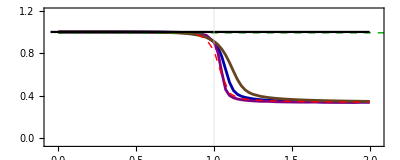

```mathematica
fig2a=Show[ListPlot[{DatCocR50,DatCocR100,DatCocR25},Joined->True,Frame->True,PlotRange->{{-0.05,2.05},{-0.05,1.2}},PlotStyle->{{Darker[Blue],Thickness[0.005]},{Purple,Thickness[0.005]},{Darker[Brown],Thickness[0.005]}},LabelStyle->{Black,12},GridLines->{{1},{}},GridLinesStyle->{Red,{}}],ListPlot[DataCoCat,Joined->True,PlotStyle->{Red,Dashed,Thick}],ListPlot[DataCoZq,Joined->True,PlotStyle->{Darker[Green],Dashed,Thick}],Plot[1.0,{x,-0.05,2},PlotStyle->{Black}],AspectRatio->0.4]
```

```mathematica
Export["Trvsg.png",fig2a]
```

Trvsg.png

#### (b)

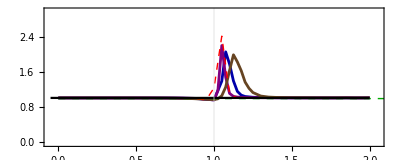

```mathematica
fig2b=Show[ListPlot[{DatCocPR50,DatCocPR100,DatCocPR25},Joined->True,Frame->True,PlotRange->{{-0.05,2.05},{-0.05,3}},PlotStyle->{{Darker[Blue],Thickness[0.005]},{Purple,Thickness[0.005]},{Darker[Brown],Thickness[0.005]}},LabelStyle->{Black,12},GridLines->{{1},{}},GridLinesStyle->{Red,{}}],ListPlot[DataCoCat2,Joined->True,PlotRange->All,PlotStyle->{Red,Dashed,Thick}],ListPlot[DataCoZq2,Joined->True,PlotStyle->{Darker[Green],Dashed,Thick}],Plot[1.0,{x,-0.05,2},PlotStyle->{Black}],AspectRatio->0.4]
```

```mathematica
Export["TrPvsg.png",fig2a]
```

TrPvsg.png

#### (c)

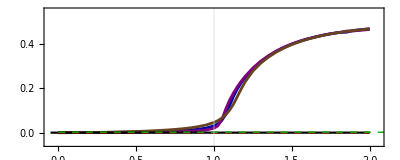

```mathematica
fig2c=Show[ListPlot[{DatImpR50,DatImpR100,DatImpR25},Joined->True,Frame->True,PlotRange->{{-0.05,2.05},{-0.05,0.55}},PlotStyle->{{Darker[Blue],Thickness[0.005]},{Purple,Thickness[0.005]},{Darker[Brown],Thickness[0.005]}},LabelStyle->{Black,12},GridLines->{{1},{}},GridLinesStyle->{Red,{}}],Plot[0.0,{x,-0.05,2},PlotStyle->{Black}],ListPlot[DataImpCat,Joined->True,PlotRange->All,PlotStyle->{Red,Dashed,Thick}],ListPlot[DataImpZq,Joined->True,PlotRange->All,PlotStyle->{Darker[Green],Dashed,Thick}],AspectRatio->0.4]
```

```mathematica
Export["Impvsg.png",fig2c]
```

Impvsg.png

#### (d)

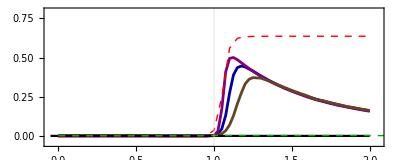

```mathematica
fig2d=Show[ListPlot[{DatNegR50,DatNegR100,DatNegR25},Joined->True,Frame->True,PlotRange->{{-0.05,2.05},{-0.05,0.8}},PlotStyle->{{Darker[Blue],Thickness[0.005]},{Purple,Thickness[0.005]},{Darker[Brown],Thickness[0.005]}},LabelStyle->{Black,12},GridLines->{{1},{}},GridLinesStyle->{{Red},{}}],Plot[0.0,{x,-0.05,2},PlotStyle->{Black}],ListPlot[DataNegCat,Joined->True,PlotRange->All,PlotStyle->{Red,Dashed,Thick}],ListPlot[DataNegZq,Joined->True,PlotRange->All,PlotStyle->{Darker[Green],Dashed,Thick}],AspectRatio->0.4]
```

```mathematica
Export["Negvsg.png",fig2d]
```

Negvsg.png

#### (e)

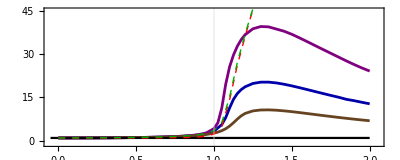

```mathematica
fig2e=Show[ListPlot[{DatQFIdisR50,DatQFIdisR100,DatQFIdisR25},Joined->True,Frame->True,PlotRange->{{-0.05,2.05},{-1.0,45}},PlotStyle->{{Darker[Blue],Thickness[0.005]},{Purple,Thickness[0.005]},{Darker[Brown],Thickness[0.005]}},LabelStyle->{Black,12},GridLines->{{1},{}},GridLinesStyle->{{Red},{}}],Plot[1.0,{x,-0.05,2},PlotStyle->{Black}],ListPlot[DataQFIdisCat,Joined->True,PlotRange->All,PlotStyle->{Red,Dashed,Thick}],ListPlot[DataQFIdiszq,Joined->True,PlotRange->All,PlotStyle->{Darker[Green],Dashed,Thick}],AspectRatio->0.4]
```

```mathematica
Export["QFIdisvsg.png",fig2e]
```

QFIdisvsg.png

#### (f)

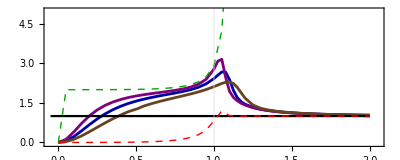

```mathematica
fig2f=Show[ListPlot[{QFIPR50,QFIPR100,QFIR25},Joined->True,Frame->True,PlotRange->{{-0.05,2.05},{-0.05,5}},PlotStyle->{{Darker[Blue],Thickness[0.005]},{Purple,Thickness[0.005]},{Darker[Brown],Thickness[0.005]}},LabelStyle->{Black,12},GridLines->{{1},{}},GridLinesStyle->{{Red},{}}],Plot[1.0,{x,-0.05,2},PlotStyle->{Black}],ListPlot[DataQFICat,Joined->True,PlotRange->All,PlotStyle->{Red,Dashed,Thick}],ListPlot[DataQFIzq,Joined->True,PlotRange->All,PlotStyle->{Darker[Green],Dashed,Thick}],AspectRatio->0.4]
```

```mathematica
Export["QFIvsg.png",fig2f]
```

QFIvsg.png